# 3-band flattened nonsingular: self-consistency, Ds and Tc

### Def: bloch state

```mathematica
a[J_,m_,k_,phi_]:=k^J Cos[J phi]
```

```mathematica
b[J_,m_,k_,phi_]:=k^J Sin[J phi]
```

Bloch states:

```mathematica
uplus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uplusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

```mathematica
u0[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],I m,a[J,m,k,phi]}
```

```mathematica
u0dag[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],-I m,a[J,m,k,phi]}
```

```mathematica
uminus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uminusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

### Def: quasiparticle energy

quasiparticle band at μ=0:

```mathematica
quasiplusns[eg_,delta_]:=Sqrt[eg^2+delta^2]
```

```mathematica
quasi0ns[eg_,delta_]:=delta
```

```mathematica
quasiminusns[eg_,delta_]:=Sqrt[eg^2+delta^2]
```

## secant to solve gap equation

### Def: gap eq at T=0

compute U from the gap equation

```mathematica
uans[J_,m_,eg_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2/(2quasiplusns[eg,delta])+Abs[u0[J,m,k,phi][[1]]]^2/(2quasi0ns[eg,delta])+Abs[uminus[J,m,k,phi][[1]]]^2/(2quasiminusns[eg,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

```mathematica
ubns[J_,m_,eg_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2/(2quasiplusns[eg,delta])+Abs[u0[J,m,k,phi][[2]]]^2/(2quasi0ns[eg,delta])+Abs[uminus[J,m,k,phi][[2]]]^2/(2quasiminusns[eg,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

### calculation

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(i-1)+0.0001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=uaf[J,m];
ubvalue=ubf[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

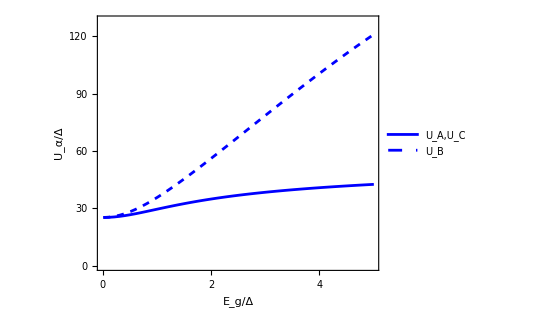

```mathematica
small3bandf=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,128}},
PlotStyle->{Blue,{Blue,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,
FrameTicks->{{{0,30,60,90,120},None},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ","U_α/Δ"},
PlotLegends->Placed[LineLegend[{Style["U_A,U_C",15],Style["U_B",15]},LegendLayout->"Row"], {0.5,0.13}],
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
J=1;delta=0.1;
mlist=Table[0.01(i-1)+0.001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=uaf[J,m];
ubvalue=ubf[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

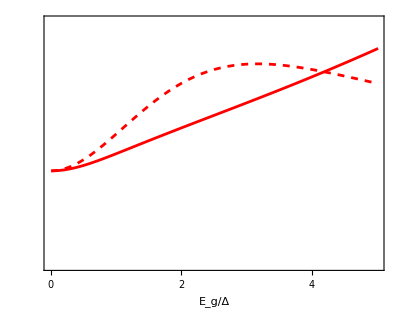

```mathematica
large3bandf=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,65}},
PlotStyle->{Red,{Red,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,FrameTicks->{{None,{0,20,40,60}},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ",""},
(*PlotLegends->Placed[{"U_A","U_B"}, {0.3,0.8}],*)
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
uplot3bandf=Overlay[{small3bandf,large3bandf}]
```

-Graphics--Graphics-

```mathematica
Export["3bandUf.pdf",uplot3bandf]
```

3bandUf.pdf

### Def: secant method solve Δ from fixed U_A, U_B at finite T

```mathematica
newtonA3bandns[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uA/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2 Tanh[quasiplusns[eg,deltaavg]/(2temp)]/(2quasiplusns[eg,deltaavg])+Abs[u0[J,m,k,phi][[1]]]^2Tanh[quasi0ns[eg,deltaavg]/(2temp)]/(2quasi0ns[eg,deltaavg])+Abs[uminus[J,m,k,phi][[1]]]^2Tanh[quasiminusns[eg,deltaavg]/(2temp)]/(2quasiminusns[eg,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB3bandns[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uB/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2 Tanh[quasiplusns[eg,deltaavg]/(2temp)]/(2quasiplusns[eg,deltaavg])+Abs[u0[J,m,k,phi][[2]]]^2Tanh[quasi0ns[eg,deltaavg]/(2temp)]/(2quasi0ns[eg,deltaavg])+Abs[uminus[J,m,k,phi][[2]]]^2Tanh[quasiminusns[eg,deltaavg]/(2temp)]/(2quasiminusns[eg,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant3bandnsstep[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA3bandns,newtonB3bandns};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],temp,uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],temp,uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],temp,uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant3bandns[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95,secant3bandnsstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### example calculation

m=0 is always uniform

```mathematica
J=1;m=0.1;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
temp=0.0001;eg=0;
secant3bandns[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.53125,Null}

damping factor is 1.

deltas are {0.1,0.1}

```mathematica
uA
uB
```

2.51327

2.51327

```mathematica
J=1;m=0.1;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
temp=0.01;eg=0.1;
secant3bandns[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.8125,Null}

damping factor is 0.972986

deltas are {0.0783597,0.0606502}

as Eg becomes larger

```mathematica
J=1;m=0.42;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
temp=0.01;eg=0.3;
secant3bandns[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{1.03125,Null}

damping factor is 0.982784

deltas are {0.0414064,0.0415786}

m=0.42 is the optimal UPC value

```mathematica
J=1;m=0.42;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
temp=0.01;eg=0.1;
secant3bandns[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{0.703125,Null}

damping factor is 0.980455

deltas are {0.0724018,0.0724869}

```mathematica
J=1;m=0.42;egvalue=0.2;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

3.9824

3.9752

```mathematica
J=6;m=0.42;egvalue=0.2;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

4.87164

2.9135

```mathematica
J=6;m=0.1;egvalue=0.2;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

4.26115

3.51603

```mathematica
J=6;m=0.001;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

2.51327

2.51327

```mathematica
J=6;m=0;egvalue=0.5;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

4.20239

12.8152

```mathematica
J=6;m=0.1;egvalue=0.5;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

6.22887

4.29431

```mathematica
J=6;m=0.032;egvalue=0.5;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

5.4106

5.42573

```mathematica
J=6;m=0.032;egvalue=0.8;delta=0.1;
uA=uans[J,m,egvalue]
uB=ubns[J,m,egvalue]
```

6.03437

6.05487

```mathematica
J=6;m=0.032;egvalue=0;delta=0.1;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
temp=0.01;eg=0.1;
secant3bandns[delta,delta]//Timing
Print["damping factor is ",alpha];
Print["deltas are ",{deltaA,deltaB}];
```

{3.54688,Null}

damping factor is 0.986777

deltas are {0.0724238,0.0723575}

### Def: show how uniform as E_g and T changes

```mathematica
howuniform3bandns[egstep_,eglength_,tempstep_,templength_]:=(
egvalue=0;(*J and delta are given outside, to use function uA and uB*)
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[egstep(i-1),{i,1,eglength}];
templist=Table[tempstep(i-1)+0.0001,{i,1,templength}];
deltaavgtable=ConstantArray[0,{eglength,templength}];
deltaratiotable=ConstantArray[0,{eglength,templength}];
(*{deltaA,deltaB}={delta,delta};*)
For[iofeg=1,iofeg<eglength+1,iofeg++,
eg=eglist[[iofeg]];
For[ioftemp=1,ioftemp<templength+1,ioftemp++,
temp=templist[[ioftemp]];
secant3bandns[delta,delta];(*use previous output as new input to save iteration steps*)
deltaavgtable[[iofeg,ioftemp]]=(2deltaA+deltaB)/3;
deltaratiotable[[iofeg,ioftemp]]=deltaA/deltaB;
];
];
)
```

### Δ=0.1, m=0.1 calculation***

```mathematica
J=1;delta=0.1;m=0.42;
egstep=0.05;eglength=11;tempstep=0.004;templength=11;
howuniform3bandns[egstep,eglength,tempstep,templength]//Timing
```

{86.0313,Null}

```mathematica
deltaavg3dplot01=ListPlot3D[Flatten[Table[{eglist[[i]],templist[[j]],deltaavgtable[[i,j]]},{i,1,eglength},{j,1,templength}],1],
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ̄"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
(*Export["avg3dplot01.pdf",deltaavg3dplot01]*)
```

avg3dplot01.pdf

```mathematica
deltaratio3dplot01=ListPlot3D[Flatten[Table[{eglist[[i]],templist[[j]],deltaratiotable[[i,j]]},{i,1,eglength},{j,1,templength}],1],
PlotRange->{0.9,1.1},
AxesLabel->{"E_g/ε_Λ","T/ε_Λ","Δ_A/Δ_B"},
LabelStyle->Directive[Black,15],
Mesh->Full,Boxed->False,ViewPoint->{1.5,-1,1},
ImageSize->300]
```

-Graphics3D-

```mathematica
(*Export["ratio3dplot01.pdf",deltaratio3dplot01]*)
```

ratio3dplot01.pdf

```mathematica
uA
uB
```

2.51327

2.51327

## Ds vs m calculation

### Def: quantum metric

choose c(m)=m:

```mathematica
(* QM of the middle band*)
g0xx[J_,m_,k_]:=J^2 k^(2J-2)(m^2+k^(2J)/2)/(m^2+k^(2J))^2
```

### Def: Ds at T=0, numerical (μ=0):

the integral below excludes a factor Δ:

```mathematica
(*the T=0 function is in unit of delta, while the finite-T one is not, careful!*)
```

```mathematica
ds3bandns[J_?NumericQ,eg_?NumericQ,delta_?NumericQ]:=4NIntegrate[(k/(2π))(1-delta/quasiplusns[eg,delta])g0xx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### Def: Ds at T=0, analytical (μ=0):

```mathematica
chif[t_]:=1-1/Sqrt[1+t^2]
```

```mathematica
Fflat[J_,λm_]:=(J/(2π))(1-λm^2-2Log[λm])
```

### Def: Ds of finite temp (for μ=0 only)

coherence factors:

between 0 and up band:

```mathematica
p0upplusns[eg_,deltat_]:=(1/2)(1+deltat/quasiplusns[eg,deltat])
```

```mathematica
p0upminusns[eg_,deltat_]:=(1/2)(1-deltat/quasiplusns[eg,deltat])
```

```mathematica
ds3bandnstemp[J_?NumericQ,eg_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=4deltat^2NIntegrate[(k/(2π))(Tanh[quasi0ns[eg,deltat]/(2temp)]/quasi0ns[eg,deltat]+Tanh[quasiplusns[eg,deltat]/(2temp)]/quasiplusns[eg,deltat]-2p0upplusns[eg,deltat](Tanh[quasi0ns[eg,deltat]/(2temp)]+Tanh[quasiplusns[eg,deltat]/(2temp)])/(quasi0ns[eg,deltat]+quasiplusns[eg,deltat])-2p0upminusns[eg,deltat](Tanh[quasi0ns[eg,deltat]/(2temp)]-Tanh[quasiplusns[eg,deltat]/(2temp)])/(quasi0ns[eg,deltat]-quasiplusns[eg,deltat]))g0xx[J,m,k],{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]
```

test the function ds3bandftemp (compare with the T=0 function ds3bandf):

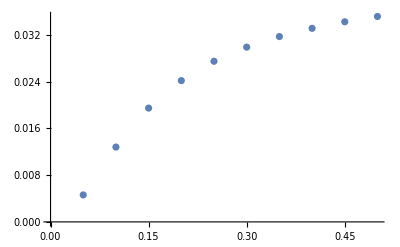

```mathematica
J=1;temp=0.0001;delta=0.1;m=0.42;
ListPlot[Table[{0.05i,delta ds3bandns[J,0.05i,delta]},{i,1,10}]]
```

```mathematica
J=1;temp=0.0001;delta=0.1;m=0.42;
ListPlot[Table[{0.05i,ds3bandnstemp[J,0.05i,delta,temp]},{i,1,10}]]
```

-Graphics-

the two completely match!

### J=1, Δ=0.1 and 0.5, numerical calculation***

```mathematica
(*delta=0.1*)
J=1;temp=0.0001;delta=0.1;m=0.42;
eglist=Table[0.01(i-1)+0.001,{i,1,101}];
dslist={};
For[ieg=1,ieg<Length[eglist]+1,ieg++,
eg=eglist[[ieg]];
dstotvalue=ds3bandnstemp[J,eg,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata01ns=Table[{eglist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[eglist]}];
```

{0.,Null}

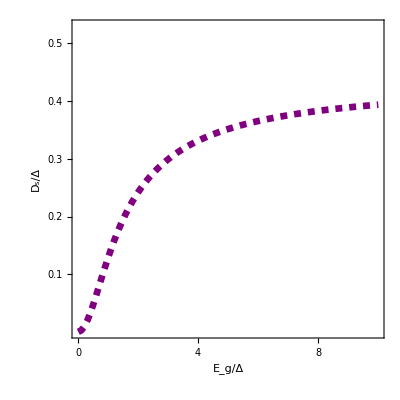

```mathematica
dsvseg01=ListPlot[dsdata01ns,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,10},{0,0.53}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3,0.4,0.5},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.72,0.92}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

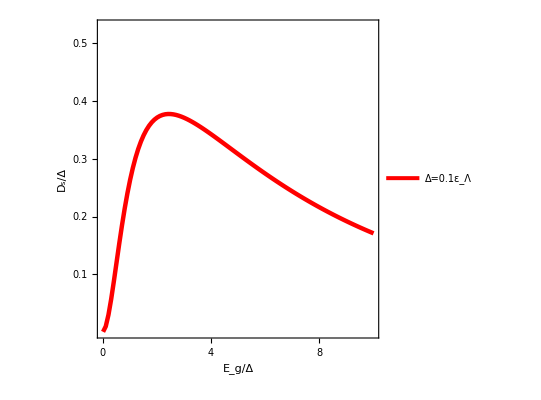
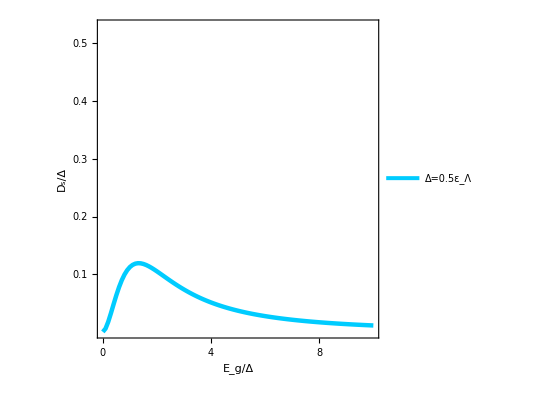
-Graphics--Graphics--Graphics-

```mathematica
dsfplot=Overlay[{dsvsm01,dsvsm05,dsvseg01}]
```

```mathematica
Export["dsvsm3bandf.pdf",dsfplot]
```

dsvsm3bandf.pdf

### J=6, m=0.42, Δ=0.1 and 0.5, numerical calculation***

```mathematica
(*delta=0.1*)
J=6;temp=0.0001;delta=0.1;m=0.42;
eglist=Table[0.01(i-1)+0.001,{i,1,101}];
dslist={};
For[ieg=1,ieg<Length[eglist]+1,ieg++,
eg=eglist[[ieg]];
dstotvalue=ds3bandnstemp[J,eg,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata01ns=Table[{eglist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[eglist]}];
```

{0.0625,Null}

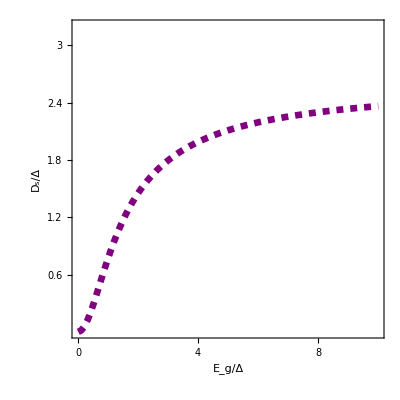

```mathematica
dsvseg01=ListPlot[dsdata01ns,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,10},{0,3.2}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],Style["D_s/Δ",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.6,1.2,1.8,2.4,3},None},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.72,0.92}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

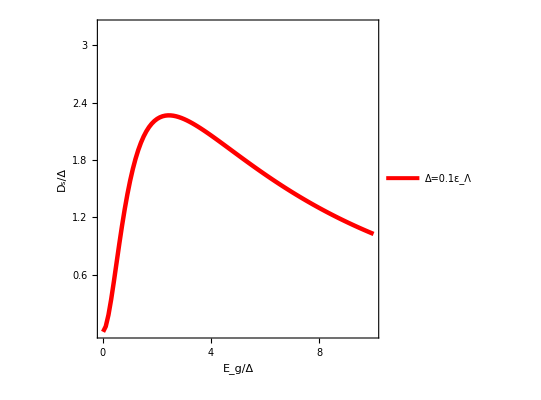
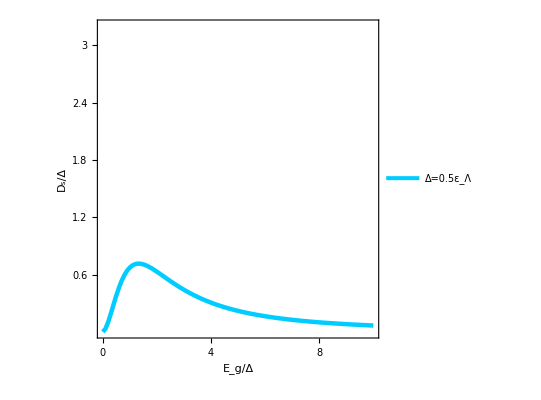
-Graphics--Graphics--Graphics-

```mathematica
dsfplot=Overlay[{dsvsm01,dsvsm05,dsvseg01}]
```

```mathematica
Export["dsvsm3bandfJ6.pdf",dsfplot]
```

dsvsm3bandfJ6.pdf

### J=6, m=0.032, Δ=0.1 and 0.5, numerical calculation***

```mathematica
(*delta=0.1*)
J=6;temp=0.0001;delta=0.1;m=0.032;
eglist=Table[0.01(i-1)+0.001,{i,1,101}];
dslist={};
For[ieg=1,ieg<Length[eglist]+1,ieg++,
eg=eglist[[ieg]];
dstotvalue=ds3bandnstemp[J,eg,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata=Table[{eglist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[eglist]}];
```

{0.015625,Null}

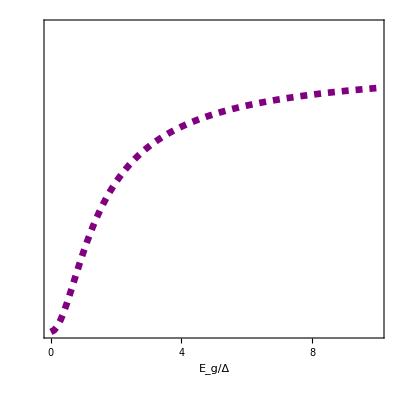

```mathematica
dsvseg01=ListPlot[dsdata,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,10},{0,8.5}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],(*Style["D_s/Δ",18]*)None},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{None,{2,4,6,8}},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.72,0.92}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
dsfplot=Overlay[{dsvsm01,dsvsm05,dsvseg01}]
```

-Graphics--Graphics--Graphics-

```mathematica
Export["dsvsm3bandfj6.pdf",dsfplot]
```

dsvsm3bandfj6.pdf

```mathematica
(*delta=0.5*)
J=6;temp=0.0001;delta=0.5;m=0.032;
eglist=Table[0.05(i-1)+0.005,{i,1,101}];
dslist={};
For[ieg=1,ieg<Length[eglist]+1,ieg++,
eg=eglist[[ieg]];
dstotvalue=ds3bandnstemp[J,eg,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata=Table[{eglist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[eglist]}];
```

{0.,Null}

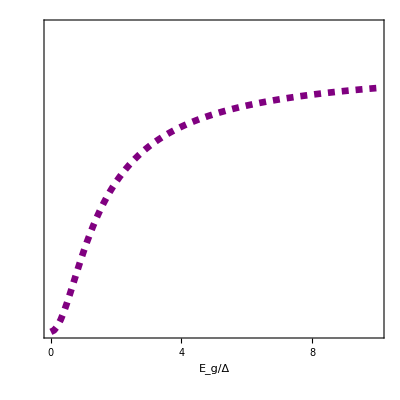

```mathematica
dsvseg05=ListPlot[dsdata,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,10},{0,8.5}},
Frame->True,FrameLabel->{Style["E_g/Δ",18],(*Style["D_s/Δ",18]*)None},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{None,{2,4,6,8}},{{0,2,4,6,8,10},None}},
LabelStyle->Directive[16],
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",20]}],{0.72,0.92}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

### other plots

```mathematica
(*delta=0.5*)
J=1;temp=0.0001;delta=0.5;m=0.42;
eglist=Table[0.05(i-1)+0.001,{i,1,101}];
dslist={};
For[ieg=1,ieg<Length[eglist]+1,ieg++,
eg=eglist[[ieg]];
dstotvalue=ds3bandnstemp[J,eg,delta,temp];
AppendTo[dslist,dstotvalue];
]//Timing
dsdata05ns=Table[{eglist[[j]]/delta,dslist[[j]]/delta},{j,1,Length[eglist]}];
```

{0.1875,Null}

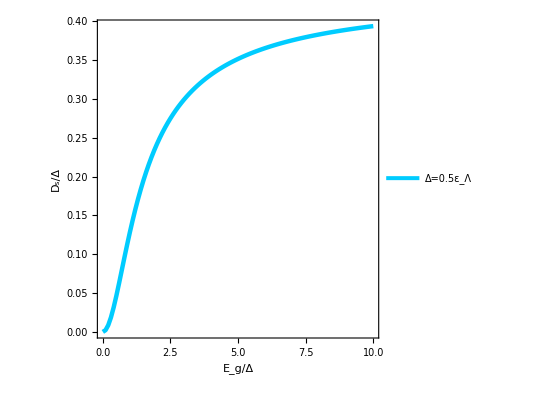

```mathematica
dsvseg05=ListPlot[dsdata05ns,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},(*PlotRange->{{0,10},{0,4.2}},*)
Frame->True,FrameLabel->{Style["E_g/Δ",23],Style["D_s/Δ",23]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{1,2,3,4},None},{{0,2,4,6,8,10},None}},*)
LabelStyle->Directive[Black, 22],
PlotLegends->Placed[LineLegend[{Style["Δ=0.5ε_Λ",20]}],{0.72,0.92}],
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
Export["dsvsm3bandf.pdf",dsvsm]
```

dsvsm3bandf.pdf

## 3-dim secant to find Tc

### Def: 3-dim secant method

```mathematica
bkteq3bandns[deltaA_?NumericQ,deltaB_?NumericQ,temp_?NumericQ,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(π/8)ds3bandnstemp[J,eg,deltaavg,temp]-temp
)
```

```mathematica
(*input two temps and return a new temp*)
tc3bandnsstep[{deltaA0_,deltaB0_,temp0_},{deltaA1_,deltaB1_,temp1_}]:=(
input0={deltaA0,deltaB0,temp0};
input1={deltaA1,deltaB1,temp1};
functionlist={newtonA3bandns,newtonB3bandns,bkteq3bandns};
jacobian=ConstantArray[0,{3,3}];
For[i=1,i<4,i++,
For[j=1,j<4,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],changelist1[[3]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],input1[[3]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],input1[[3]],uA,uB],{k,1,3}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
tc3bandns[inputdeltaA_,inputdeltaB_,inputtemp_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB,inputtemp};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.98&&outputlist1[[3]]>tcmin,tc3bandnsstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
temp=outputlist1[[3]]
)
```

```mathematica
J=1;egvalue=0;delta=0.1;m=0.42;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eg=0.1;temptrial=0.01;
tc3bandns[delta,delta,temptrial]//Timing
```

{0.125,0.00514534}

### J=1, Δ=0.1 and 0.5 calculation***

```mathematica
J=1;egvalue=0;delta=0.1;m=0.42;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.025(i-1)+0.01,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.01;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,tc3bandns[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
(*temptrial=temp;*)
(*here Tc of the first Eg value is very small, so the trial Tc should be set to higher value (as constant 0.01 here)*)
]//Timing
tcdata01ns=Table[{eglist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@eglist}];
```

{5.67188,Null}

```mathematica
(*J=1;egvalue=0;delta=0.5;m=0.42;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.125i+0.05,{i,1,20}];
inputtemp=0.01;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,bkt3bandnssecant[inputtemp]];
inputtemp=tempfinal;
]//Timing
data05=Table[{eglist[[i]],tbktlist[[i]]},{i,1,Length@eglist}];*)
```

{73.3906,Null}

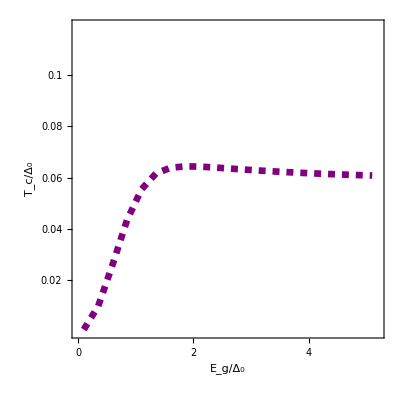

```mathematica
tc01ns=ListPlot[tcdata01ns,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,5.2},{0,0.119}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.02,0.04,0.06,0.08,0.1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
(*PlotMarkers->{{shape1,0.03}},*)
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

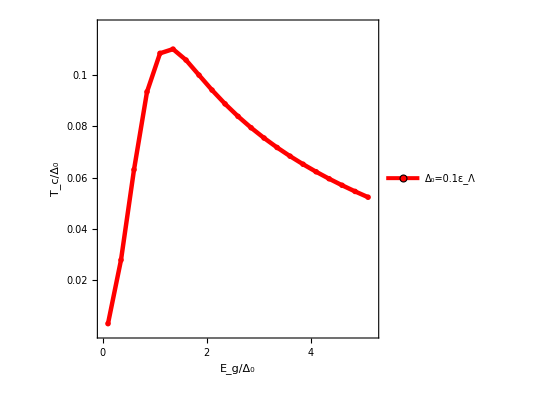
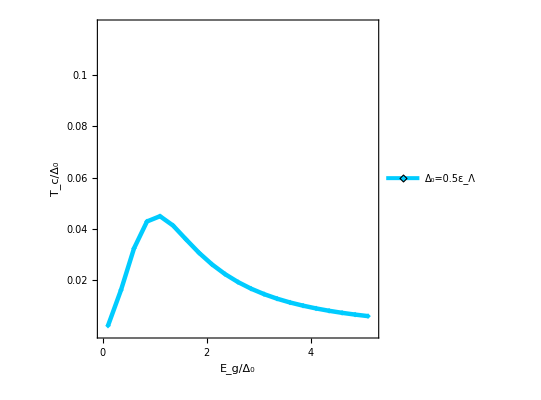
-Graphics--Graphics--Graphics-

```mathematica
tcfplot=Overlay[{tc01,tc05,tc01ns}]
```

```mathematica
Export["tc3bandfJ1.pdf",tcfplot]
```

tc3bandf.pdf

```mathematica
(*tc05ns=ListPlot[data05,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},(*PlotRange->{{0,2.5},{0,0.025}},*)
Frame->True,FrameLabel->{"",Style["T_c/ε_Λ",23]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.005,0.01,0.015,0.02},None},{None,{0,0.5,1,1.5,2,2.5}}},*)
LabelStyle->Directive[Black, 22],
PlotMarkers->{{shape2,0.03}},
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]*)
```

```mathematica
(*tcplot=Overlay[{tc01,tc05}]*)
```

### J=6, m=0.42, Δ=0.1 and 0.5 calculation***

```mathematica
J=6;egvalue=0;delta=0.1;m=0.42;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.025(i-1)+0.01,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.02;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,tc3bandns[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
(*temptrial=temp;*)
(*here Tc of the first Eg value is very small, so the trial Tc should be set to higher value (as constant 0.01 here)*)
]//Timing
tcdata01ns=Table[{eglist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@eglist}];
```

{205.875,Null}

```mathematica
(*J=1;egvalue=0;delta=0.5;m=0.42;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.125i+0.05,{i,1,20}];
inputtemp=0.01;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,bkt3bandnssecant[inputtemp]];
inputtemp=tempfinal;
]//Timing
data05=Table[{eglist[[i]],tbktlist[[i]]},{i,1,Length@eglist}];*)
```

{73.3906,Null}

```mathematica
tcdata01ns
```

{{0.1,0.00513412},{0.35,0.0598526},{0.6,0.153356},{0.85,0.218525},{1.1,0.235884},{1.35,0.228167},{1.6,0.214906},{1.85,0.203421},{2.1,0.194336},{2.35,0.187367},{2.6,0.181926},{2.85,0.177587},{3.1,0.174059},{3.35,0.171138},{3.6,0.168685},{3.85,0.166597},{4.1,0.164799},{4.35,0.163236},{4.6,0.161864},{4.85,0.160652},{5.1,0.159572}}

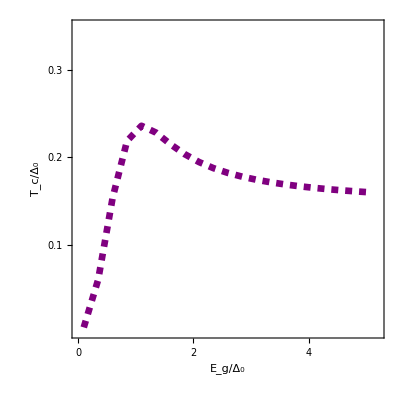

```mathematica
tc01nsm042=ListPlot[tcdata01ns,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,5.2},{0,0.35}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
(*PlotMarkers->{{shape1,0.03}},*)
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

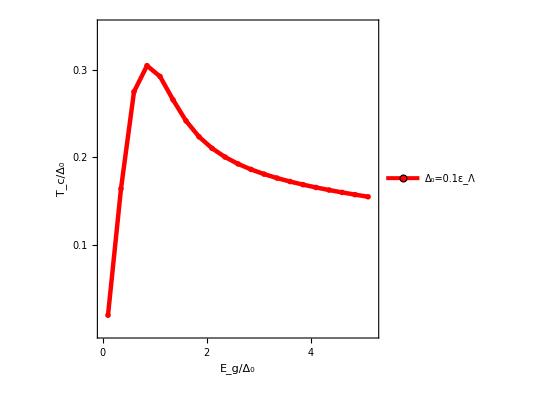
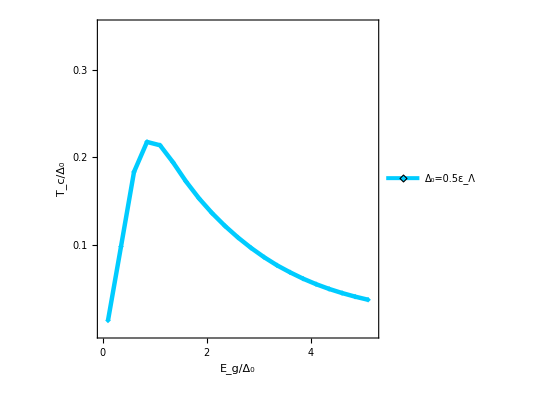
-Graphics--Graphics--Graphics-

```mathematica
tcfplot=Overlay[{tc01,tc05,tc01nsm042}]
```

```mathematica
Export["tc3bandfJ6m042.pdf",tcfplot]
```

tc3bandfJ6m042.pdf

```mathematica
(*tc05ns=ListPlot[data05,
Joined->True,
PlotStyle->{{RGBColor[0,0.8,1],Thickness[0.008]}},(*PlotRange->{{0,2.5},{0,0.025}},*)
Frame->True,FrameLabel->{"",Style["T_c/ε_Λ",23]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.005,0.01,0.015,0.02},None},{None,{0,0.5,1,1.5,2,2.5}}},*)
LabelStyle->Directive[Black, 22],
PlotMarkers->{{shape2,0.03}},
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]*)
```

```mathematica
(*tcplot=Overlay[{tc01,tc05}]*)
```

### J=6, m=0.032, Δ=0.1 calculation***

```mathematica
J=6;egvalue=0;delta=0.1;m=0.032;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.025(i-1)+0.01,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.02;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,tc3bandns[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
(*temptrial=temp;*)
(*here Tc of the first Eg value is very small, so the trial Tc should be set to higher value (as constant 0.01 here)*)
]//Timing
tcdata01ns=Table[{eglist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@eglist}];
```

{180.578,Null}

```mathematica
tcdata01ns
```

{{0.1,0.0147238},{0.35,0.166219},{0.6,0.29635},{0.85,0.328554},{1.1,0.313897},{1.35,0.284283},{1.6,0.258096},{1.85,0.23929},{2.1,0.225533},{2.35,0.21612},{2.6,0.208871},{2.85,0.203157},{3.1,0.198561},{3.35,0.194795},{3.6,0.191658},{3.85,0.189006},{4.1,0.186735},{4.35,0.184768},{4.6,0.183049},{4.85,0.181533},{5.1,0.180187}}

```mathematica
tcdatans={{0.1,0.014723754874338926},{0.35000000000000003,0.16621897193341845},{0.6000000000000001,0.29635000020743973},{0.8500000000000001,0.32855367717518374},{1.1,0.3138970045676173},{1.35,0.2842834880632806},{1.6000000000000003,0.25809560120830566},{1.8500000000000003,0.23929020736416215},{2.1,0.22553305591089798},{2.35,0.21611970769074718},{2.6,0.20887099609221707},{2.8500000000000005,0.2031572337205798},{3.1000000000000005,0.19856094892737214},{3.35,0.1947954245280992},{3.6000000000000005,0.1916584045164143},{3.85,0.1890060401849204},{4.1000000000000005,0.18673467102951913},{4.3500000000000005,0.1847680283422012},{4.6000000000000005,0.18304883363910313},{4.8500000000000005,0.18153325484234994},{5.1,0.18018719719391504}};
```

```mathematica
(*J=1;egvalue=0;delta=0.5;m=0.42;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.125i+0.05,{i,1,20}];
inputtemp=0.01;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,bkt3bandnssecant[inputtemp]];
inputtemp=tempfinal;
]//Timing
data05=Table[{eglist[[i]],tbktlist[[i]]},{i,1,Length@eglist}];*)
```

{73.3906,Null}

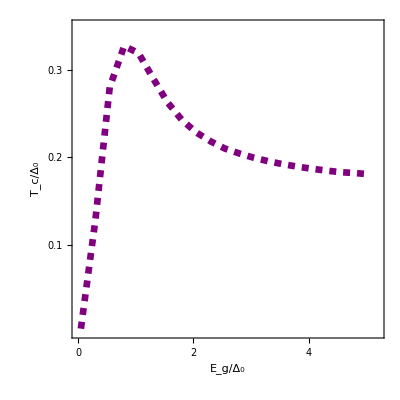

```mathematica
tc01nsm0032=ListPlot[tcdatans,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,5.2},{0,0.35}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
(*PlotMarkers->{{shape1,0.03}},*)
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
tcfplot=Overlay[{tc01,tc05,tc01nsm0032}]
```

-Graphics--Graphics--Graphics-

```mathematica
Export["tc3bandfj6m0032.pdf",tcfplot]
```

tc3bandfj6m0032.pdf

### J=6, m=0.032, Δ=0.5 calculation***

```mathematica
J=6;egvalue=0;delta=0.5;m=0.032;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.125(i-1)+0.025,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
temptrial=0.02;
tbktlist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
AppendTo[tbktlist,tc3bandns[deltaAtrial,deltaBtrial,temptrial]];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
(*temptrial=temp;*)
(*here Tc of the first Eg value is very small, so the trial Tc should be set to higher value (as constant 0.01 here)*)
]//Timing
tcdatans=Table[{eglist[[i]]/delta,tbktlist[[i]]/delta},{i,1,Length@eglist}];
```

{134.688,Null}

```mathematica
tcdatans
```

{{0.05,0.00369237},{0.3,0.127314},{0.55,0.280072},{0.8,0.327167},{1.05,0.319042},{1.3,0.290439},{1.55,0.262866},{1.8,0.242587},{2.05,0.228305},{2.3,0.218037},{2.55,0.209734},{2.8,0.204148},{3.05,0.199287},{3.3,0.195303},{3.55,0.191978},{3.8,0.189163},{4.05,0.18675},{4.3,0.184659},{4.55,0.182831},{4.8,0.181802},{5.05,0.18042}}

```mathematica
tc05nsj6=ListPlot[tcdatans,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,5.2},{0,0.35}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["T_c/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.1,0.2,0.3},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
(*PlotMarkers->{{shape1,0.03}},*)
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

-Graphics-

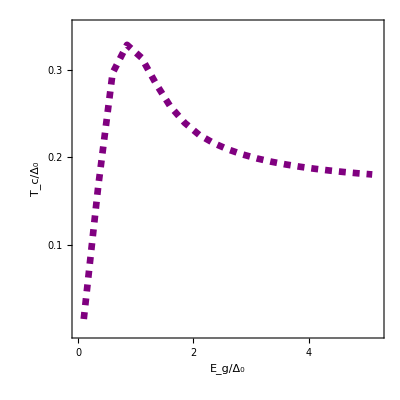
-Graphics--Graphics--Graphics-

```mathematica
tcfplot=Overlay[{tc01,tc05,tc01nsJ6m0032}]
```

```mathematica
Export["tc3bandfJ6m042.pdf",tcfplot]
```

tc3bandfJ6m042.pdf

## 2-dim secant to find T=0 SC gap vs Eg

### Def: T=0 secant for SC gap

```mathematica
newtonA3bandnst0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(uA/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2 /(2quasiplusns[eg,deltaavg])+Abs[u0[J,m,k,phi][[1]]]^2/(2quasi0ns[eg,deltaavg])+Abs[uminus[J,m,k,phi][[1]]]^2/(2quasiminusns[eg,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaA
)
```

```mathematica
newtonB3bandnst0[deltaA_?NumericQ,deltaB_?NumericQ,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
(uB/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2 /(2quasiplusns[eg,deltaavg])+Abs[u0[J,m,k,phi][[2]]]^2/(2quasi0ns[eg,deltaavg])+Abs[uminus[J,m,k,phi][[2]]]^2/(2quasiminusns[eg,deltaavg])),{phi,0,2π},{k,0,1},PrecisionGoal->5,AccuracyGoal->5,MaxRecursion->200,Method->"GlobalAdaptive"]-deltaB
)
```

```mathematica
secant3bandnsstept0[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA3bandnst0,newtonB3bandnst0};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],uA,uB],{k,1,2}];
alpha=1/(1+Norm[inversetimes]/Norm[input1]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant3bandnst0[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.0001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95&&inputdeltaA>0.0001,secant3bandnsstept0[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

### J=6, Δ=0.1, T=0 SC gap vs Eg***

```mathematica
J=6;egvalue=0;delta=0.1;m=0.032;tcmin=0.0001;
uA=uans[J,m,egvalue];
uB=ubns[J,m,egvalue];
eglist=Table[0.025(i-1)+0.005,{i,1,21}];
deltaAtrial=delta;
deltaBtrial=delta;
deltalist={};
For[whicheg=1,whicheg<Length@eglist+1,whicheg++,
eg=eglist[[whicheg]];
secant3bandnst0[deltaAtrial,deltaBtrial];
AppendTo[deltalist,(2deltaA+deltaB)/3];
deltaAtrial=deltaA;
deltaBtrial=deltaB;
]//Timing
data01ns=Table[{eglist[[i]]/delta,deltalist[[i]]/delta},{i,1,Length@eglist}];
```

{22.6875,Null}

```mathematica
uA
uB
```

2.51327

2.51327

```mathematica
data01ns
```

{{0.05,0.999168},{0.3,0.971127},{0.55,0.902723},{0.8,0.8071},{1.05,0.705517},{1.3,0.620826},{1.55,0.559886},{1.8,0.517584},{2.05,0.487606},{2.3,0.466582},{2.55,0.449576},{2.8,0.436289},{3.05,0.425698},{3.3,0.417069},{3.55,0.409906},{3.8,0.403865},{4.05,0.398704},{4.3,0.394244},{4.55,0.390352},{4.8,0.386925},{5.05,0.383887}}

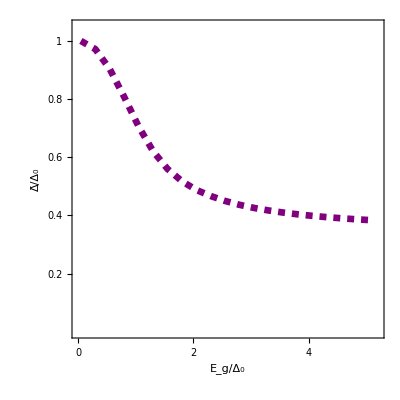

```mathematica
gap01fns=ListPlot[data01ns,
Joined->True,
PlotStyle->{{Purple,Thickness[0.012],Dashed}},PlotRange->{{0,5.2},{0,1.05}},
Frame->True,FrameLabel->{Style["E_g/Δ_0",18],Style["Δ̄/Δ_0",18]},
FrameStyle->Directive[Thickness[0.007]],
FrameTicks->{{{0.2,0.4,0.6,0.8,1},None},{{0,1,2,3,4,5},None}},
LabelStyle->Directive[16],
(*PlotMarkers->{{shape1,0.03}},*)
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

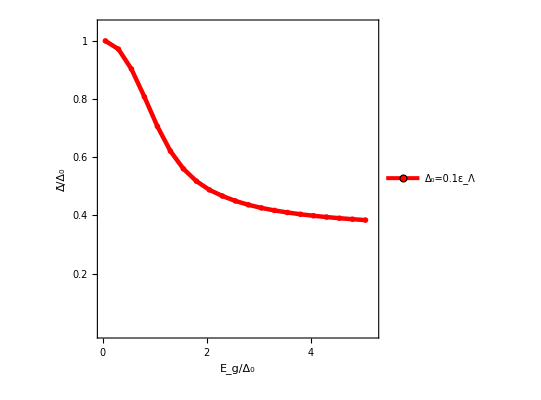
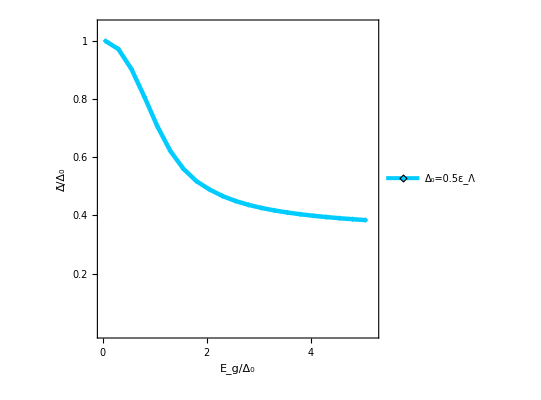
-Graphics--Graphics--Graphics-

```mathematica
gapfplot=Overlay[{gap01f,gap05f,gap01fns}]
```

```mathematica
Export["gap3bandfj6.pdf",gapfplot]
```

gap3bandfj6.pdf